## Annihilations

```mathematica
Clear["Global`*"];
ClearSystemCache[];
SetDirectory[NotebookDirectory[]];
```

```mathematica
tempConversion = (1*^-9/(1.16*^4)); (* GeV *)
NM     = (0.939); (* GeV *)
SOL   = 299792458.; (* ms^-1 *)
VELDISP  = 270.*^3;(* ms^-1 *)
NSVEL =  200.*^3 ;(* ms^-1 *)
G       =  6.67408*^-11; (*Grav Constant*)
TT = ((1*^10 * 3.154*^7)/(6.58*^-16)*1*^9); (* therm time *)
hBar = 1.054571800*^-34;


vAvg[mx_, temp_] := (6*temp*tempConversion)/mx;

capRate = 1.*^22*6.58*^-16*1*^-9; (*test cap rate*)
```

## NS Data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = 12.1;

muFn     = Interpolation[ EoSData[[All, {1,8}]] ]; (* Chemical potential in MeV *)
muFe     = Interpolation[ EoSData[[All, {1,10}]] ]; (* Chemical potential in MeV *)
muFμ     = Interpolation[ EoSData[[All, {1,11}]] ]; (* Chemical potential in MeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];

ndList = nb*Yn;
nd          = Interpolation[ Transpose[{radius,nb*Yn}]]; (* Neutron density in fm^-1*)

NSMass=   Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *)
```

```mathematica
rTh[T_, mx_]:=3.265*√(T/10^5)*√(1/mx);
```

```mathematica
ϕ[r_]:= (2*π*G*(7.76*1*^17)*r^2)/3;
```

```mathematica
ndAnFac[mx_, T_]:=NIntegrate[x^2*Exp[(-2*x^2)/rTh[T,mx]^2],{x, 0, rTh[T, mx]}]/(4*π*(NIntegrate[x^2*Exp[-x^2/rTh[T,mx]^2],{x, 0, rTh[T, mx]}])^2);
```

## Masses and Form Factors

```mathematica
lepMasses = {0.5109989461, 105.6583745, 1776.86, 0,0,0}*1.*^-3;(* {e, μ, τ,Subscript[ν, e], Subscript[ν, μ], Subscript[ν, τ]}*)
quarkMasses = {2.2*^-3, 4.7*^-3, 95*^-3, 1.257, 4.18, 173};(* {u, d, s, c, b, t}  *)
```

```mathematica
fT = {Mean[{0.019, 0.022, 0.012, 0.011, 0.014, 0.018}], Mean[{0.041, 0.049, 0.033, 0.027, 0.036, 0.042}], Mean[{0.14, 0.36, 0.053, 0.045, 0.118, 0.26}]};

fTG = 1. - Sum[fT[[n]], {n, 1, 3}];

DeltaN = {Mean[{-0.4, -0.43, -0.44, -0.43, -0.48, -0.43}],Mean[{0.77, 0.86, 0.84, 0.84, 0.78, 0.84}], Mean[{-0.12, -0.09, -0.03, -0.085, -0.15, -0.08}]};

deltaN = { 0.23,-0.84, 0.05};(* {u, d, s} *)
```

```mathematica
c12 = Sum[(NM*fT[[n]])/quarkMasses[[n]],{n, 1,3}] +(2.*fTG)/27.*(Sum[NM/quarkMasses[[n]], {n, 3, 6}] - NM);
mBar = 1./Sum[1./quarkMasses[[n]], {n, 1, 3}];
C34 = Sum[mBar/quarkMasses[[n]],{n,1,6}];
c34 = Sum[NM/quarkMasses[[n]]*(1 - C34 +mBar)*DeltaN[[n]],{n, 1,3}];
c56 = 3.;
c78 = Sum[DeltaN[[n]], {n, 1, 3}];
c910 = Sum[deltaN[[n]], {n, 1, 3}];
```

```mathematica
fde[mx_]:=HeavisideTheta[-muFe[rMin]*1*^-3 +mx];
fdμ[mx_]:=HeavisideTheta[-muFμ[rMin]*1*^-3 +mx];
fdoth[mx_] := 1.;
fdSelect[mf_]:= Which[mf == lepMasses[[1]], fde, mf == lepMasses[[2]], fdμ, True, fdoth];
```

## Cross sections

```mathematica
d1ACS[mx_, temp_] :=(Sum[(mx^2/(16.*π*c12^2))*(1. - mf^2/mx^2)^(3/2)*vAvg[mx, temp]*fdSelect[mf][mx], {mf, Select[lepMasses, #≤ mx&]}]+Sum[((3.*mx^2)/(16.*π*c12^2))*(1. - mf^2/mx^2)^(3/2)*vAvg[mx, temp], {mf, Select[quarkMasses, #≤ mx&]}] );
(*================================================================================================================================================================*)
d2ACS[mx_, temp_] :=(Sum[(1./(16.*π*c12^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(8*(1 - mf^2/mx^2)+3vAvg[mx, temp])*fdSelect[mf][mx],{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(16.*π*c12^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(8*(1 - mf^2/mx^2)+3vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d3ACS[mx_, temp_] :=(Sum[(1./(8.*π*c34^2))*mx^2*Sqrt[1. - mf^2/mx^2]*vAvg[mx, temp]*fdSelect[mf][mx],{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(8.*π*c34^2))*mx^2*Sqrt[1. - mf^2/mx^2]*vAvg[mx, temp],{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d4ACS[mx_, temp_] :=(Sum[(1./(4.*π*c34^2))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][mx](**(1. + ((2.*mx^2- mf)/(8.*(mx^2 - mf^2)))*vAvg[mx, temp])*),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π*c34^2))*mx^2*Sqrt[1. - mf^2/mx^2](**(1. +( (2.*mx^2- mf)/(8.*(mx^2 - mf^2)))*vAvg[mx, temp])*),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d5ACS[mx_, temp_] := (Sum[(1./(4.*π*c56^2))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][mx]*((2. +mf^2/mx^2) + (1./12.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π*c56^2))*mx^2 Sqrt[1. - mf^2/mx^2]*((2. +mf^2/mx^2) + (1./12.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d6ACS[mx_, temp_] :=(Sum[(1./(12.*π*c56^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(2. + mf^2/mx^2 )*vAvg[mx, temp]*fdSelect[mf][mx],{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(12.*π*c56^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(2. + mf^2/mx^2 )*vAvg[mx, temp],{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d7ACS[mx_, temp_] :=(Sum[(1./(12.*π*c78^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(24*(1 - mf^2/mx^2)+ (7 + (2*mf^2)/mx^2)*vAvg[mx, temp])*fdSelect[mf][mx],{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(12.*π*c78^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(24*(1 - mf^2/mx^2)+ (7 + (2*mf^2)/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d8ACS[mx_, temp_] := (Sum[(1./(4.*π*c78^2))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][mx]*(mf^2/mx^2 + (1./12.)*(2. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π*c78^2))*mx^2*Sqrt[1. - mf^2/mx^2]*(mf^2/mx^2 + (1./12.)*(2. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

d9ACS[mx_, temp_] := (Sum[(1./(4.*π*c910^2))*mx^2*Sqrt[1. - mf^2/mx^2]*fdSelect[mf][mx]*((7.+mf^2/mx^2) + (2./3.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[(3./(4.*π*c910^2))*mx^2*Sqrt[1. - mf^2/mx^2]*((7.+mf^2/mx^2) + (2./3.)*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);
```

## Capture Rates

```mathematica
Do[
Evaluate[Symbol[cap<>"CAP"]] =Interpolation[Import[StringJoin[{"../cap_rate/Mathematica_cap/", cap, "_cap.dat"}]]]
,
{cap, {"d0", "d1", "d2","d3","d4","d5","d6","d7", "d8", "d9", "d10"}}
]
```

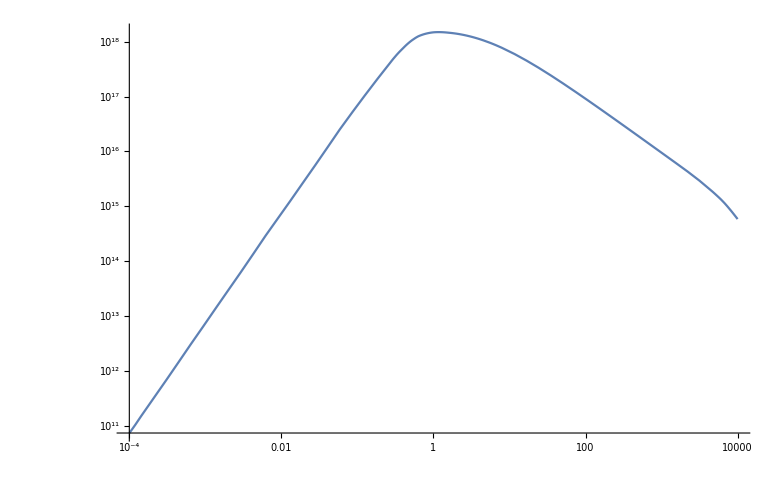

```mathematica
LogLogPlot[d10CAP[Log10[x]], {x, 1*^-4,1*^4}]
```

```mathematica
|
```

## Annihilation Rates

```mathematica
anG[ACS_,CAP_ ,mx_?NumericQ, temp_?NumericQ] :=1./((0.5*TT)^2*CAP[Log10[mx]]*ndAnFac[mx, temp]*ACS[mx, temp]);
```

```mathematica
Do[
Clear[out];

out = With[{x:=10^xp},
Table[Flatten[{x,Table[anG[ToExpression[oper<>"ACS"],ToExpression[oper<>"CAP"],  x,T], {T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}]  }],{xp, -4.8, 5, 0.05}]];
Export[StringJoin[ToString[oper], "ACS.dat"], out, "Table"]

,
{oper, {"d1","d2", "d3", "d4", "d5", "d6", "d7", "d8", "d9", "d10"}}
]
```

## Plots

InterpolatingFunction::dmval: Input value {-6.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

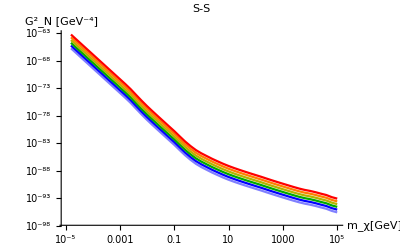

```mathematica
ssPlot = ListLogLogPlot[
 Evaluate@Table[
With[{x:=10^xp},
Table[{x,anG[d1ACS,d1CAP, x, T]*c12^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}
],

Joined->True, PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red},
AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"}, 
PlotLabel->"S-S", 
LabelStyle->Directive[Black,Bold]]
```

```mathematica
(*ppPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[d4ACS, x, T]*c34^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"PS-PS", LabelStyle->Directive[Black,Bold]]*)
```

```mathematica
(*vvPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[d5ACS, x, T]*c56^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"V-V", LabelStyle->Directive[Black,Bold]]*)
```

```mathematica
(*aaPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[d8ACS, x, T]*c78^2},{xp, -6, 6, 0.05}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"A-A", LabelStyle->Directive[Black,Bold]]*)
```

```mathematica
(*ttPlot =ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[d9ACS, x, T]*c910^2},{xp, -6, 6, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "(G^2)_N [GeV^-4]"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"T-T", LabelStyle->Directive[Black,Bold]]*)
```

```mathematica
(*groupedPlots =Legended[GraphicsGrid[{{ssPlot, ppPlot}, {vvPlot, aaPlot}, {ttPlot}}, ImageSize->Full ], LineLegend[Reverse[{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}],Reverse[{"10^1K","10^2K","10^3K","10^4K", "10^5K", "10^6K"}]]]*)
```

```mathematica
(*Export["ann-limits-fdsup.pdf", %]*)
```

## Neutrinos Stuff

```mathematica
(*ndAv = NIntegrate[x^2*nd[x]*(1*^15)^3, {x, rMin, rMax}]/NIntegrate[x^2, {x, rMin, rMax}];
Gf = 1.166*1*^-5;*)
```

```mathematica
(*l[mx_, T_] :=1/(ndAv*Gf^2*(mx + mx/8*vAvg[mx, T])^2*0.389*^-31)*1*^-3;*)
```

```mathematica
(*ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,l[x, T]/(rMax*1000)},{xp, -6, -4, 0.2}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}], Joined->True,AxesLabel->{"m_χ[GeV]", "l/R_⋆"},PlotStyle->{Lighter[Blue, 0.5], Blue, Darker[Green], Darker[Yellow, 0.3], Orange, Red}, PlotLabel->"ν m.f.p/R_⋆", LabelStyle->Directive[Black,Bold]]*)
```

```mathematica
(* *)
```